```mathematica
2+2
```

4

```mathematica
f[x_]=x∫_x^∞ BesselK[5/3,x]ⅆx;
g[x_]= x BesselK[2/3,x];
```

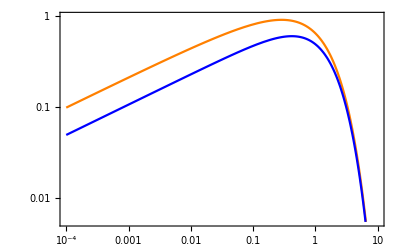

```mathematica
LogLogPlot[{f[x],g[x]},{x,10^-4,10},Frame->True,PlotStyle->{Orange,Blue}]
```

### Assymptotic expansion of modified Bessel functions for small/large z

```mathematica
KS[ν_,z_]= Gamma[ν]/2(2/z)^ν;KL[ν_,z_]= √(π/(2z))ⅇ^-z(1+(4 ν^2-1)/(8z)+((4 ν^2-1)(4 ν^2-9))/(2! 8 z^2));
```

### First the G (x) functions

```mathematica
gS[z_]=FullSimplify[z KS[2/3,z]]
gL[z_]=FullSimplify[z KL[2/3,z]]
```

Gamma[2/3]/(2^(1/3) (1/z)^(1/3))

(ⅇ^-z √(π/2) (1/z)^(3/2) (-455+18 z (7+72 z)))/1296

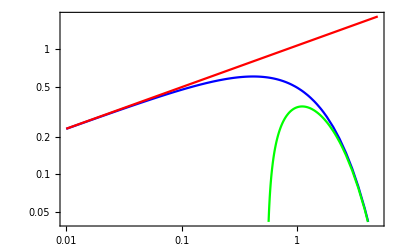

```mathematica
LogLogPlot[{g[x],gS[x],gL[x]},{x,10^-2,5},Frame->True,PlotStyle->{Blue,Red, Green}]
```

### Now the F(x) functions

```mathematica
fS[z_]=FullSimplify[z ∫_z^∞ KS[5/3,x]ⅆx, Assumptions->{z ∈ Reals,z>0}]
fL[z_]=FullSimplify[z ∫_z^∞ KL[5/3,x]ⅆx, Assumptions->{z ∈ Reals,z>0}]
```

2^(2/3) z^(1/3) Gamma[2/3]

(√(π/2) z ((91 ⅇ^-z (19+16 z))/z^(3/2)+488 √π Erfc[√z]))/1944

Now introduce an expansion of the Erfc function

```mathematica
fL2[z_]=(√(π/2) z ((91 ⅇ^-z (19+16 z))/z^(3/2)+488 √π(1/6 ⅇ^-z+1/2 ⅇ^(-(4/3)z)) ))/1944
```

(√(π/2) z (488 (1/2 ⅇ^(-4 z/3)+ⅇ^-z/6) √π+(91 ⅇ^-z (19+16 z))/z^(3/2)))/1944

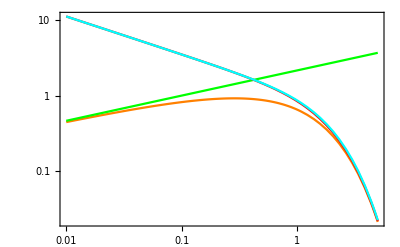

```mathematica
LogLogPlot[{f[x],fS[x],fL[x], fL2[x]},{x,10^-2,5},Frame->True,PlotStyle->{Orange,Green,Red, Cyan}]
```

### This are the small/large x expressions that are going to be used in the code

### For F (x)

```mathematica
ExpandAll[fS[x]]//N
FullSimplify[ExpandAll[fL2[x]]//N]
```

2.14953 x^(1/3)

0.278823 ⅇ^(-1.33333 x) x+(ⅇ^(-1. x) (1.1147+0.938696 x+0.092941 x^(3/2)))/(√x)

#### For G (x)

```mathematica
ExpandAll[gS[x]]//N
FullSimplify[ExpandAll[gL[x]]//N]
```

1.07476/(1/x)^(1/3)

1.25331 ⅇ^(-1. x) (1/x)^(3/2) (-0.35108+x (0.0972222+1. x))

### Now Lets do tables for a range in x between 0.01 and 5

#### Log spaced numbers

```mathematica
{a,b,c}={0.01,100,5};
t=(c/a)^(1/b)//N ;
Xlist = a*t^Range[b];
Flist := {}
Glist := {}
```

```mathematica
For[i=1,i<101,i++,{AppendTo[Flist,f[ Xlist[[i]]]],AppendTo[Glist,g[ Xlist[[i]]]]}]
```

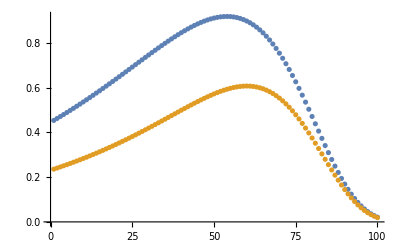

```mathematica
ListPlot[{Flist,Glist}]
```

#### Write to textfiles

```mathematica
Export["Xlist.txt",Xlist]
Export["Flist.txt",Flist]
Export["Glist.txt",Glist]
```

Xlist.txt

Flist.txt

Glist.txt